-Graphics-

# Wolfram Language

## For Physics & Astrophysics Computation

-Graphics-

## Outline

### Motivation

Necessity of computation in modern research and teaching

### Introductory Examples

Ballistics and Kinematics

Stellar Cluster Data Analysis

### Intermediate Examples

Planck Radiation Law

N-Body Simulations

### Advanced Examples

PDE Modelling in 3D

Wolfram Quantum Framework

## Motivation

### What Is Computation?

```mathematica
Function[
{data},
CellPrint[
Cell[
TextData[
MapIndexed[
StyleBox[
#1,
FontColor->If[
#2⟦1⟧<14,
RGBColor[0.0902,0.1608,0.2588],
RGBColor[0.5,0.5,0.5,1-(#2⟦1⟧)/StringLength[data]]
]
]&,
Characters[data]
]
],
"Section",
Magnification->Inherited*0.5,
CellMargins->{{Inherited*2,Inherited},{Inherited,Inherited}},
CellGroupingRules->{"OutputGrouping",30},
ShowGroupOpener->False
]
]
][StringJoin["Computation ⊃ {Vector Calculus, Kinematics, Random Processes, Fluid Mechanics, Quantum Theory, Dimensional Analysis, Control Systems, Optimisation, Reliability Analysis, PDEs, Finite Element Analysis, Signal Processing, Complex System, Fourier Analysis, Integral Transforms, Heat Transfer, Statistics, Vibrations, Wavelet Analysis…", ConstantArray[" ", 30]]
]
```

## Computation ⊃ {Vector Calculus, Kinematics, Random Processes, Fluid Mechanics, Quantum Theory, Dimensional Analysis, Control Systems, Optimisation, Reliability Analysis, PDEs, Finite Element Analysis, Signal Processing, Complex System, Fourier Analysis, Integral Transforms, Heat Transfer, Statistics, Vibrations, Wavelet Analysis…

## A Credible Vote of Confidence

```mathematica
Magnify[Row[{-Graphics-,Pane[Style["“Mathematica is the best computational tool I've used in the past 25 years.”","Subsubsection",20,Gray],400]},Spacer[10]]]
```

-Graphics-“Mathematica is the best computational tool I've used in the past 25 years.”

— Kip Thorne, astrophysicist, 2017 Nobel Prize winner and consultant for Interstellar

## Introductory Examples

### Modelling a Projectile

We can model the projectile as a point mass subject only to uniform gravity.

Newton’s second law gives:

Define our parameters:

```mathematica
θ=π/6;
v0=10;
g=QuantityMagnitude[UnitConvert[Entity["Planet","Earth"][EntityProperty["Planet","Gravity"]],"SI"]];
```

Set up the equation (with initial conditions) to solve:

```mathematica
eqs={y''[t]==-g,x''[t]==0};
inits={x'[0]==v0*Cos[θ],y'[0]==v0*Sin[θ],x[0]==0,y[0]==0};
```

Solve the system:

```mathematica
sol=NDSolve[{eqs,inits},{x,y},{t,0.,10}]
```

Visualise the trajectory:

```mathematica
ParametricPlot[
{x[t],y[t]}/.sol,
{t,0,1},
PlotLabel->"Projectile Trajectory",
AxesLabel->{"x","y"},
PlotRange->{Automatic,{0,2}}
]
```

An event corresponds to a particular time t_a crossed during the integration of eqns in NDSolve:

```mathematica
event=WhenEvent[y[t]==0,tof=t];
eventSol=
NDSolve[
{eqs,inits,event},
{x,y},
{t,0,10}
][[1]]
```

```mathematica
ParametricPlot[
{x[t],y[t]}/.eventSol,
{t,0,tof},
PlotLabel->"Time of Flight = "<>ToString[tof]<>"s",
AxesLabel->{"x","y"}
]
```

Define a function to find the ‘time-of-flight’ for a projectile:

```mathematica
findTimeOfFlight[θ_?NumericQ]:=
  Module[
{eqs,inits,event,time,sol},
    eqs={y''[t]==-g,x''[t]==0};
    inits={x'[0]==v0*Cos[θ],y'[0]==v0*Sin[θ],x[0]==0,y[0]==0};
    event=WhenEvent[y[t]==0,time=t; "StopIntegration"];
    sol=NDSolve[{eqs,inits,event},{x,y},{t,0,10}][[1]];
    time
  ]
```

Generate some data for a range of launch angles:

```mathematica
projectileData=
Table[
{θ,findTimeOfFlight[θ],v0*Cos[θ]*findTimeOfFlight[θ]},
{θ,0.02,π/2,0.02}
];
```

We want to find the launch angle that maximises the horizontal range:

```mathematica
MaximalBy[projectileData,#[[3]]&]
```

{{0.78,1.43526,10.2035}}

We can also use the built-in FindMaximum:

```mathematica
Clear[θ]
FindMaximum[v0*Cos[θ]*findTimeOfFlight[θ],{θ,0.1},AccuracyGoal->6]
```

{10.2041,{θ→0.785398}}

## Introductory Examples

### Stellar Cluster Dataset

Along with all the curated data from Wolfram|Alpha, Wolfram Language also has direct access to the Wolfram Data Repository. This is a public location where users can submit datasets that can then be used by others.

The repository is organised into categories for easy navigation. Look at the Astronomy category.

Retrieve a curated dataset of star clusters in the Milky Way:

```mathematica
clusters=ToTabular[ResourceData["Star Clusters"]]
```

```mathematica
ColumnKeys[clusters]
```

A scatter plot testing the hypothesis that older clusters tend to have lower metallicities, because they formed when the galaxy was less enriched:

```mathematica
ListPlot[
clusters->{"LogAge","Metallicity"},
Frame->True,
FrameLabel->{"LogAge","Metallicity"},
PlotMarkers->{Automatic, Tiny}
]
```

A scatter plot testing the hypothesis that dust accumulates along the line of sight, so more distant clusters have larger reddening:

```mathematica
ListPlot[
clusters->{"Distance","BVColourExcess"},
Frame->True,
FrameLabel->{"Distance (pc)","BVColourExcess"},
PlotMarkers->{Automatic, Tiny},
PlotStyle->Red
]
```

Show the distance vs apparent distance modulus relationship:

```mathematica
ListPlot[
clusters->{"Distance","ApparentDistanceModulus"},
Frame->True,
FrameLabel->{"Distance","ApparentDistanceModulus"},
PlotMarkers->{Automatic, Tiny},
PlotStyle->Black
]
```

```mathematica
ListLogLinearPlot[
clusters->{"Distance","ApparentDistanceModulus"},
PlotRange->All,
Frame->True,
FrameLabel->{"Distance","ApparentDistanceModulus"},
PlotMarkers->{Automatic, Tiny},
PlotStyle->Black
]
```

#### Plot the 3D Distribution by Age

Remove rows where the distance or age is missing:

```mathematica
nonMissingData=
ConstructColumns[
Select[clusters,! MissingQ[#Distance] && ! MissingQ[#LogAge] &],
{"Distance","RightAscension","Declination","LogAge"}
]
```

Find the position of each star cluster in the galactic frame:

```mathematica
positions=
Map[
AstroPosition[#,"Galactic"]&,
Values[
Normal[nonMissingData[[All,{"RightAscension","Declination","Distance"}]]]
]
];
```

Convert each position to Cartesian coordinates:

```mathematica
positionsCartesian=
Map[
AstroPosition[#,"Galactic","Cartesian"]&,
positions
];
```

While the unit is sometimes displayed in light years or kilo-light years, distances are stored using astronomical units:

```mathematica
With[
{star=RandomChoice[positionsCartesian]},
Echo[{star,star["Data"]}];
Map[
UnitConvert[
Quantity[#,"AstronomicalUnit"],
"KilolightYears"
]&,
star["Data"]
]
]
```

Convert from astronomical units to kilo-parsecs. The first Part of each AstroPosition is the co-ordinates:

```mathematica
convertPositionsCartesian=
Map[
QuantityMagnitude[
UnitConvert[
Quantity[#,"AstronomicalUnit"],
"Kiloparsecs"]
]&,
positionsCartesian[[All,1]]
];
```

Plot and colour the points by their age:

```mathematica
ListPointPlot3D[
Map[List,convertPositionsCartesian],
PlotStyle->Map[ColorData["Rainbow"],Rescale[Normal[nonMissingData[All,"LogAge"]]]],
PlotLegends->BarLegend[{"Rainbow",MinMax[nonMissingData[All,"LogAge"]]},LegendLabel->"LogAge"],
AxesLabel->{"x (kpc)","y (kpc)","z (kpc)"},
PlotRange->{{-30,39},{-17,20},{-20,20}}
]
```

-Graphics3D-

#### AstroGraphics

AstroGraphics constructs maps of any region of the sky, as viewed on any date from anywhere in the solar system:

```mathematica
AstroGraphics[
Entity["StarCluster","NGC6380"],
AstroBackground->"GalacticSky",AstroReferenceFrame->"Equatorial"
]
```

-Graphics-

## Intermediate Examples

### Properties of the Planck Radiation Law

Visualise the spectral radiance for the radiation emitted by a body at 5000 degrees Celsius, as a function of wavelength:

```mathematica
srPlot=PlanckRadiationLaw[Quantity[5000, "DegreesCelsius"],"SpectralPlot"]
```

Determine the peak and mean wavelengths as well as the colour of the body:

```mathematica
{peak,mean,color}=
Map[
N[PlanckRadiationLaw[Quantity[5000, "DegreesCelsius"],#]]&,
{"MaxWavelength","MeanWavelength","Color"}
]
```

Compare the visible spectrum with the distribution of spectral radiance for 5000 degrees Celsius:

```mathematica
Show[
ParametricPlot[
{x,y},
{x,0,2*10^-6},{y,0,10^14},
PlotPoints->100,
ColorFunction->Function[{x,y,u},ColorData["VisibleSpectrum"][x 10^9]],
ColorFunctionScaling->False
],
srPlot,

]
```

Define the Wien distribution law and Rayleigh–Jeans’s law:

```mathematica
wienDistributionLaw[T_,ν_]:=
Quantity[2,("PlanckConstant")/(("SpeedOfLight")^2*"Steradians")]*ν^3*Exp[-(Quantity[1,("PlanckConstant")/("BoltzmannConstant")]*ν)/T];
rayleighJeansLaw[T_,ν_]:=
Quantity[2,("BoltzmannConstant")/(("SpeedOfLight")^2*"Steradians")]*ν^2*T;
```

Also relevant here are the functions FormulaLookup and FormulaData!

```mathematica
Grid[
{
{"Wein Distribution Law",wienDistributionLaw[QuantityVariable["T","Temperature"],QuantityVariable["ν","Frequency"]]},{"Rayleigh–Jeans' Law",rayleighJeansLaw[QuantityVariable["T","Temperature"],QuantityVariable["ν","Frequency"]]},
{"Planck's Radiation Law",Last[FormulaData[{"PlanckRadiationLaw","Frequency"}]]}
},
Frame->All,Alignment->Left,FrameStyle->LightGray,ItemStyle->{{"Text"},Automatic}
]
```

Compute the values of the three formulas at 7000 K over the span of 10^13 to 10^15 Hz:

```mathematica
wienData=
Table[
{
10^x,
QuantityMagnitude[
wienDistributionLaw[Quantity[7000,"Kelvins"],Quantity[10^x,"Hertz"]],
("Watts")/("Hertz"*("Meters")^2*"Steradians")
]
},
{x,13,15,0.1}
];
rayleighJeansData=
Table[
{
10^x,
QuantityMagnitude[
rayleighJeansLaw[Quantity[7000,"Kelvins"],Quantity[10^x,"Hertz"]],
("Watts")/("Hertz"*("Meters")^2*"Steradians")
]
},
{x,13,15,0.1}
];
planckData=
Table[
{
10^x,
QuantityMagnitude[PlanckRadiationLaw[Quantity[7000,"Kelvins"],Quantity[10^x,"Hertz"]]]
},
{x,13,15,0.1}
];
```

```mathematica
ListLogLogPlot[
{wienData,rayleighJeansData,planckData},
Joined->True,Frame->True,Axes->False,FrameLabel->{Quantity[None,"Hertz"],Quantity[None,("Watts")/("Hertz" ("Meters")^2 "Steradians")]},PlotLegends->{"Wien Distribution Law","Rayleigh-Jeans's Law","Planck's Radiation Law"}
]
```

## Intermediate Examples

### N-Body Simulations

Simulate a number of objects that are being attracted by gravity:

```mathematica
tMax=5; nBodies=5;
simData=
NBodySimulation[
"InverseSquare",
MapThread[
<|"Mass"->1,"Position"->#1,"Velocity"->#2|>&,
{
RandomReal[{-1,1},{nBodies,3}],
RandomReal[0.1*{-1,1},{nBodies,3}]
}
],
tMax
]
```

Show the trajectories of all objects:

```mathematica
trajectories=
ParametricPlot3D[
Evaluate[simData[All,"Position",t]],
{t,0,tMax},
SphericalRegion -> True
]
```

Create an animation with tracer lines:

```mathematica
Manipulate[
Show[
ParametricPlot3D[
Evaluate[simData[All,"Position",t]],
{t,0,tCurrent},
PerformanceGoal-> "Quality",
PlotRange->PlotRange[trajectories]
],
Graphics3D[
{
PointSize[0.02],
Point[simData[All,"Position",tCurrent]]
}
]
],
{{tCurrent, 0.01, "Time"},0.01, tMax,0.1, Exclusions -> 0},
ControlType -> LabeledSlider,SaveDefinitions->True
]
```

#### Periodic Planar Orbits

In 1993, a zero angular momentum solution to the three-body problem was found, with three equal masses moving around a figure-eight shape:

```mathematica
T=10.;
figure8=
NBodySimulation[
"InverseSquare",
{<|"Mass"->1,"Position"->{0.97000436,-0.24308753,0.},"Velocity"->{0.4662036850,0.4323657300,-0.}|>,<|"Mass"->1,"Position"->{-0.97000436,0.24308753,0.},"Velocity"->{0.4662036850,0.4323657300,0.}|>,<|"Mass"->1,"Position"->{0.,0.,0.},"Velocity"->{-0.93240737,-0.86473146,0}|>},
T
];
Manipulate[
Show[
ParametricPlot3D[
Evaluate[figure8[All,"Position",t]],
{t,0,tCurrent},
PerformanceGoal-> "Quality",
PlotRange->Automatic
],
Graphics3D[
{
PointSize[0.02],
Point[figure8[All,"Position",tCurrent]]
}
]
],
{{tCurrent, 0.01, "Time"},0.01, T,0.1, Exclusions -> 0},
ControlType -> LabeledSlider,SaveDefinitions->True
]
```

See this community post and this Wolfram Demonstration!

## Advanced Examples

### Solving PDEs over 3D Regions

We have been steadily building up symbolic PDE modelling capabilities across all the standard domains.

For example, one might want to model the magnetic field around a permanent magnet or a current-carrying coil.

First, set up the variables and parameters for a cylindrical current-carrying wire (magnetic potential is zero except the z component ):

```mathematica
rAir=0.2;
rWire=0.01;
airRegion=DiscretizeRegion[Disk[{0,0},rAir]];
wireRegion=Disk[{0,0},rWire];
Je0=100000;
pars=
<|
"ElectricalConductivity"->Piecewise[{{5.9*^7,RegionMember[wireRegion][{x,y}]}},0],
"RelativePermeability"->1,
"ExternalCurrentSource"->{0,0,Piecewise[{{Je0,RegionMember[wireRegion][{x,y}]}}]}
|>;
vars={{0,0,Az[x,y]},{x,y}};
```

Now we can set up the PDE:

```mathematica
op=MagneticPDEComponent[vars,pars];
Γzero=MagneticPotentialCondition[x^2+y^2>=rAir^2,vars,pars];
pde={op==0,Γzero}
```

Solve the PDE:

```mathematica
AzFun=NDSolveValue[pde ,Az,{x,y} ∈ airRegion]
```

Find the curl of  to give . Take the  and  components:

```mathematica
bField=Curl[{0,0,AzFun[x,y]},{x,y,z}][[1 ;; 2]]
```

Finally, visualise the field:

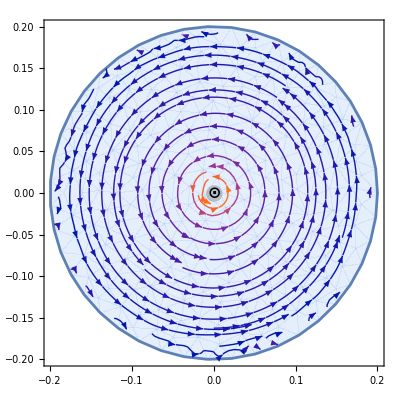

```mathematica
Show[
  StreamPlot[Evaluate[bField],{x,y} ∈ airRegion],
  Graphics[{Opacity[0.2],wireRegion,Opacity[1],Inset[Style["⊙",16,Black,Bold],{0,0}]}]
]
```

We can see that this field is entirely azimuthal about the z axis. Therefore, the field due to a circular, current-carrying coil is the sum of lots of fields like this.

The z axis is now through the centre of the coil:

```mathematica
rCoil=0.5;
tCoil=0.05;
Graphics3D[{FilledTorus[{0,0,0},{rCoil-tCoil,rCoil}],Arrow[{{0,0,-0.2},{0,0,0.2}}]},Boxed->False]
```

-Graphics3D-

This superposition of fields results in a net magnetization in the +z direction within the bounds of the coil, which enables us to solve a magnetostatic PDE with this feature.

Again, set up the variables and parameters:

```mathematica
vars={Vm[x,y,z],{x,y,z}};
rCoil=0.5;
tCoil=0.05;
coil=FilledTorus[{0,0,0},{rCoil-tCoil,rCoil}];
{xBounds,yBounds,zBounds}=RegionBounds[coil];
pars=<|"Magnetization"->{0,0,Piecewise[{{1*^5,zBounds[[1]]<=z<=zBounds[[2]]&&x^2+y^2<=(rCoil-tCoil)^2}},0]}|>
```

Use a 3D MeshRegion for the air around the coil:

```mathematica
mesh=-Graphics3D-;
```

Set up and solve this new PDE:

```mathematica
Subscript[Γ, p]=MagneticPotentialCondition[x^2+y^2+z^2>=2^2,vars,pars];
op=MagnetostaticPDEComponent[vars,pars];
```

```mathematica
VmFun=NDSolveValue[{op==0,Subscript[Γ, p]},Vm,{x,y,z}∈mesh]
```

Finally, visualise the field and compare to the previous plot:

```mathematica
Show[
Graphics3D[
{LightGray,coil}
],
StreamPlot3D[
Evaluate[-Grad[VmFun[x,y,z],{x,y,z}]],{x,-1,1},{y,-1,1},{z,-1,1},
StreamMarkers->"Arrow",StreamPoints->Coarse
],
Boxed->False
]
```

-Graphics3D-

## Advanced Examples

### Quantum Framework

High-level symbolic representation of quantum bases, states and operators

Model and simulate quantum circuits and algorithms

Interoperate with many external quantum platforms and send queries to quantum processing units from a Wolfram Notebook

Install and load the QuantumFramework paclet:

```mathematica
PacletInstall["Wolfram/QuantumFramework"]
Needs["Wolfram`QuantumFramework`"]
```

#### Basis Transformation of Quantum States

Define a 2D quantum state in the computational basis:

```mathematica
ψ1=QuantumState[{1,ⅈ}]
```

```mathematica
ψ1["Formula"]
```

Transform it into the Pauli-X basis and show the formula:

```mathematica
ψ2=QuantumState[ψ1,"X"];
ψ2["Formula"]
```

Test that the states are still the same, i.e. only the coordinates representing it in a basis have changed:

```mathematica
ψ1==ψ2
```

```mathematica
QuantumMeasurementOperator["Z"][ψ2]
```

```mathematica
QuantumMeasurementOperator["Z"][ψ1]
```

Let’s look at another example, with a more complicated quantum basis.

Define a random state in the Schwinger basis:

```mathematica
ψ3=QuantumState["RandomPure",QuantumBasis["Schwinger"]]
```

```mathematica
ψ3["Formula"]
```

Transform the state into a new basis:

```mathematica
ψ4=QuantumState[ψ3,{2,2}]
ψ4["Formula"]
```

Test that the states are still the same:

```mathematica
ψ3==ψ4
```

#### Numeric Evolution of a Quantum State

In the Wolfram Quantum Framework, quantum objects and operations can be defined symbolically and also numerically. In this regard, time evolution of quantum systems can be treated both symbolically and numerically.

Given a time-independent Hamiltonian as ,  find the quantum state at a later time, with |ψ_0⟩ = |0⟩:

```mathematica
ψf=QuantumEvolve[QuantumOperator[0.2"X"+0.8"Y"],{t,0,3}]
```

Visualise the trajectory in a Bloch sphere:

```mathematica
Manipulate[ψf[t]["BlochPlot"],{t,0,3,0.1}]
```

```mathematica
ListPlot[
Transpose[Table[ψf[t]["BlochCartesianCoordinates"],{t,0,3,0.1}]],
Joined->True,PlotLegends->{"x","y","z"},
PlotLabel->"Bloch Cartesian Coordinates",
GridLines->Automatic,
FrameLabel->{"Time (0.1s)",None},
Frame->True,AspectRatio->1/2
]
```

## Summary

Unified solution for physics and astrophysics students, researchers and professionals

State-of-the-art symbolic and numerical computation

Access to real-world data

Powerful and immediate visualisation tools

## Next Steps

#### Become a Wolfram Language User

Start a free 15-day trial

Check if you have access through your organisation here

Explore interactive courses on Wolfram U

## References

See our Public Resources here

Physics-specific guide

Astronomy Core Area page

The Wolfram Physics Project

SetOptions[EvaluationNotebook[],WindowTitle→ "Wolfram Language for Physics and Astrophysics Computation"]